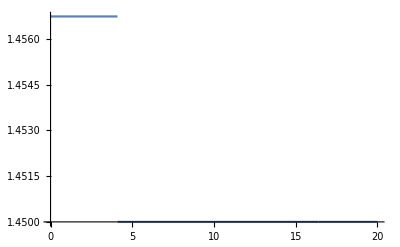

```mathematica
Clear["Global`*"]

dCore=8.2;
NA=0.14;
λ=1.55;
nMat=1.45;
β0=2Pi nMat/λ;

CalcWindow=20;(*mkm*)
N0=127;
h=5;

n[r_]:=Piecewise[{{Sqrt[nMat^2+NA^2],0≤r<dCore/2},{nMat,dCore/2≤r<2dCore},{Sqrt[nMat^2-0.0005I],2dCore≤r}}]

Plot[Re[n[r]],{r,0,CalcWindow}]
```

```mathematica
nArr=Array[n[Sqrt[#1^2+#2^2]]&,{N0,N0},{{-CalcWindow,CalcWindow},{-CalcWindow,CalcWindow}}];
StartBeam=Array[Piecewise[{{1,0≤(#1^2+#2^2)<(dCore/2)^2},{0,(dCore/2)^2≤(#1^2+#2^2)}}]&,{N0,N0},{{-CalcWindow,CalcWindow},{-CalcWindow,CalcWindow}}];

D2Fourier=(Pi/CalcWindow)^2 RotateLeft[Array[(#1^2+#2^2)&,{N0,N0},{-(N0-1)/2,-(N0-1)/2}],{(N0-1)/2,(N0-1)/2}];
FourierOp=Exp[I/β0/2 D2Fourier h];
SpatialOp=Exp[-I/2/β0 (2 Pi/λ)^2 (nArr^2-nMat^2) h];
```

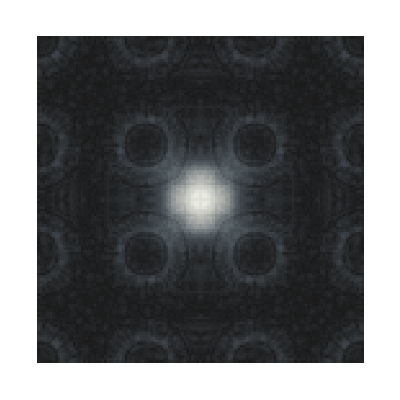

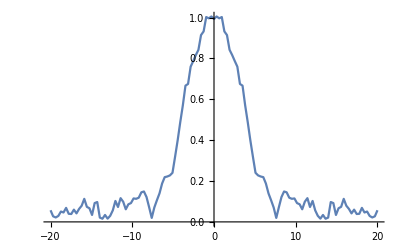

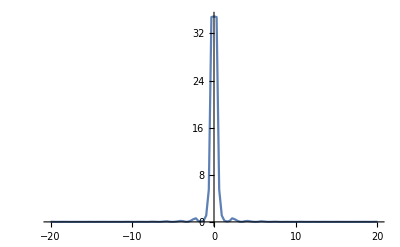

```mathematica
Beam=InverseFourier[Sqrt[FourierOp]Fourier[StartBeam]];
Monitor[
For[ξ=0.5h,ξ<100h,ξ+=h,

Beam=InverseFourier[FourierOp Fourier[Beam SpatialOp]];

],{ξ,ListPlot[Abs[Beam[[(N0+1)/2]]],Joined->True,DataRange-> {-CalcWindow,CalcWindow},PlotRange->{ {-CalcWindow,CalcWindow},All},ImageSize->Large]}]
Beam=InverseFourier[Fourier[Beam]/Sqrt[FourierOp]];

ArrayPlot[Abs[Beam],DataRange->All,ColorFunction->"GrayTones"]

ListPlot[Abs[Beam[[(N0+1)/2]]],Joined->True,DataRange-> {-CalcWindow,CalcWindow},PlotRange->{All,All}]
ListPlot[Abs[RotateRight[Abs[Fourier[Beam]],{(N0-1)/2,(N0-1)/2}][[(N0+1)/2]]]^2,Joined->True,DataRange-> {-CalcWindow,CalcWindow},PlotRange->{All,All}]
```

Домашнее задание
1) Найти установившийся пучок в волокне (моду). Параметры волокна приведены в задаче.
	Сформулировать и реализовать критерий того, что мода установилась и можно заканчивать цикл
	Подобрать оптимальный шаг дискретизации по z, по пространству и по Фурье-пространству для обеспечения приемлемой сходимости метода. Какие критерии и правила подбора использовались?
	Также подобрать диаметр и Im(n) поглощающего кольца типа ступенька так, чтобы мода устанавливалась как можно быстрее, при этом не испытывала значительного затухания. К каким артефактам моделирования приводят неоптимальные значения этих параметров поглощающего кольца?
	Придумать аподизацию (функцию пространственного фильтра), которая бы наилучшим образом реализовывала утекание излучения в модели. Проверить работу данного фильтра в каком-либо проверочном модельном эксперименте. Например, можно запустить гауссов пучок в однородную среду. Для него известна зависимость затухания интенсивности I(x,y,z). Сравнить с рассчитанной функцией затухания по методу FFT-BPM. Определить пределы параметров пучка и задачи, в которых можно считать, что фильтр работает корректно.
	Сравнить моду, найденную методом FFT-BPM. С решением задачи на собственные значения из семинара 1.
2) Дать определение идеальной тонкой линзы. Сделать оператор идеальной тонкой линзы. Проверить его работу для гауссовых пучков различного диаметра перетяжки и ее положения.
3) Придумать функцию следующих параметров. Функция возвращает массив случайных величин длиной N, таких, что:
	производная (дискретная) возвращаемой функции не более DER
	и либо среднеквадратичное отклонение чисел от нуля = RMS
	и либо максимальное отклонение чисел от нуля = PP
4) На выходе из какой-то оптической системы измерен профиль пучка - гауссов, ДМП = 5мм, λ = 1064 мм, пучок коллимирован. Также из геометрического анализа аберраций системы (например, в программе Zemax) известна и дана функция зависимости фазы пучка от радиуса. Для моделирования в качестве фазы взять случайную функцию из п.4
	найти M2 данного пучка, определив его угол расходимости в дальней зоне путем разложения по плоским волнам (преобразоваение Фурье)
	построить гистограмму распределения M2 для различных функций фазы с одинаковыми параметрами DER, RMS и PP	
5) Замоделировать “mode cleaner” или “spatial filter”. Объяснить как он работает и почему. На входе - гауссов пучок шумом по амплитуде и/или фазе, линзы - тонкие.
-Graphics-